```mathematica
vals=Import["daily_vals.tsv"];
```

```mathematica
p1=ListPlot[(#1⟦6;;7⟧&)/@vals,PlotStyle->{Black},AspectRatio->1];
```

```mathematica
medslope=ArcSin[Median[((#1⟦7⟧)/(#1⟦6⟧)&)/@vals]];
```

```mathematica
p2=Plot[{medslope x,Sin[Pi/4]*x},{x,Min[0,Min[(#1⟦6⟧&)/@vals]],Max[(#1⟦6⟧&)/@vals]},PlotStyle->{{Thick,Red},{Thick,Green}},AspectRatio->1];
```

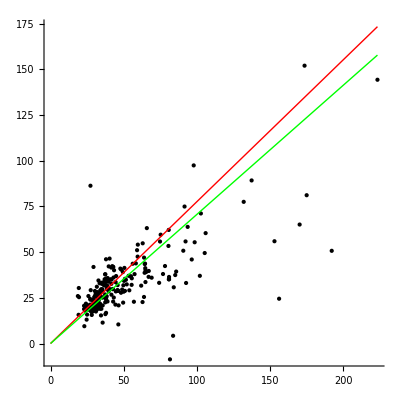

```mathematica
Show[p1,p2]
```

```mathematica
{Sin[Pi/4]//N,medslope}
```

{0.707107,0.776801}

```mathematica
yvals=Import["yearly_vals.tsv"];
```

```mathematica
p3=ListPlot[(#1⟦6;;7⟧&)/@yvals,PlotStyle->{Black},AspectRatio->1];
```

```mathematica
ymedslope=ArcSin[Median[((#1⟦7⟧)/(#1⟦6⟧)&)/@yvals]];
```

```mathematica
p4=Plot[{ ymedslope x,Sin[Pi/4]x},{x,Min[0,Min[(#1⟦6⟧&)/@yvals]],Max[(#1⟦6⟧&)/@yvals]},PlotStyle->{{Thick,Red},{Thick,Green}},AspectRatio->1];
```

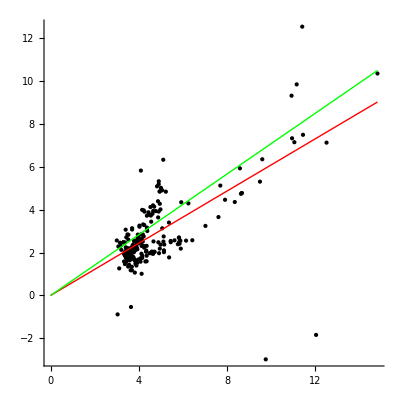

```mathematica
Show[p3,p4]
```

```mathematica
{Sin[Pi/4]//N,ymedslope}
```

{0.707107,0.60805}